# GK

## viscosity

### p_0=3.825 ,T=0.0025

```mathematica
testData3825=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00250000_waitingTime10000_idx"<>ToString[i]<>".nc","Data"],{i,10,19}];
```

```mathematica
sacfInterp3825=Table[Interpolation[Transpose[{Normal[testData3825[[i,2]]],Normal[testData3825[[i,1]]]}],Method->"Spline"],{i,10}];
```

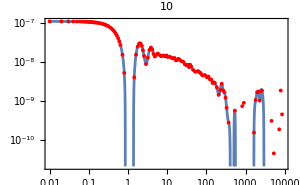
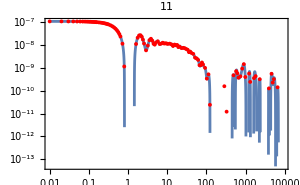
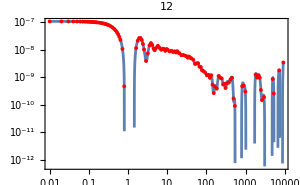
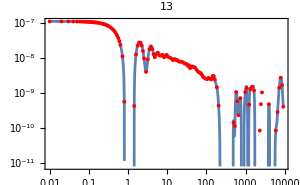
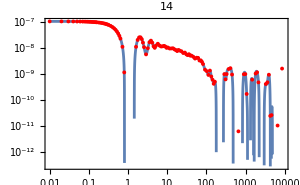
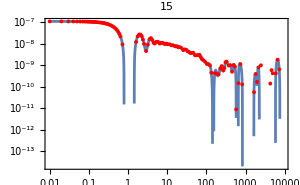
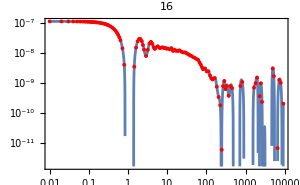
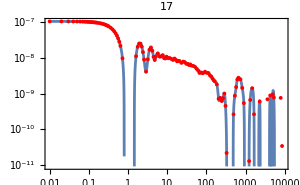

```mathematica
Table[Show[LogLogPlot[sacfInterp3825[[id]][x],{x,0.01,Last[testData3825[[id,2]]]},ImageSize->300,PlotLabel->ToString[id+9]],ListLogLogPlot[Table[{testData3825[[id,2,i]],testData3825[[id,1,i]]},{i,Length[testData3825[[id,1]]]}],PlotStyle->Red]],{id,Length[testData3825]}]
```

```mathematica
cutoff3825={370,120,150,200,150,130,250,200,200,290};
```

```mathematica
viscosity3825=Table[NIntegrate[sacfInterp3825[[i]][x],{x,0,cutoff3825[[i]]}],{i,10}]*4096/0.0025
```

{2.19131,0.837302,0.90464,1.37316,1.01182,0.809538,1.52704,1.47446,1.57014,1.31538}

```mathematica
Mean[viscosity3825]
```

1.30148

```mathematica
StandardDeviation[viscosity3825]/Sqrt[10]
```

0.135358

### p_0=3.825 ,T=0.0020

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00200000_waitingTime10000_idx12.nc"]
```

{/firstValue,/secondValue}

```mathematica
sac3825=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00200000_waitingTime10000_idx"<>ToString[i]<>".nc","Data"],{i,10,19}];
```

```mathematica
sacfInterpSAC3825=Table[Interpolation[Transpose[{Normal[sac3825[[i,2]]],Normal[sac3825[[i,1]]]}],Method->"Spline"],{i,10}];
```

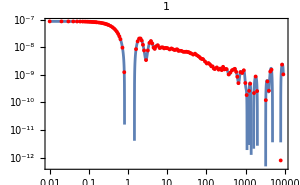
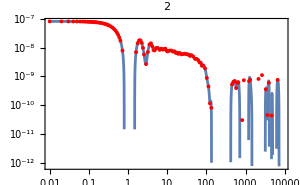
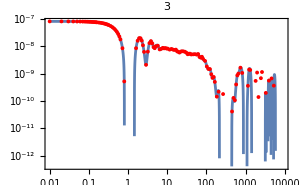
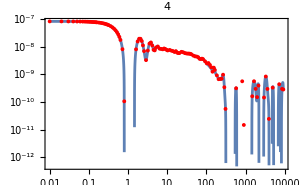
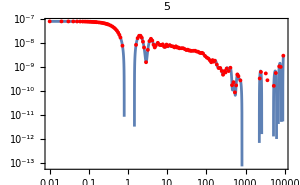
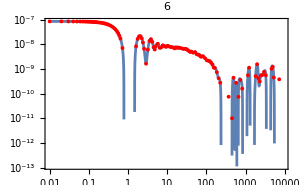
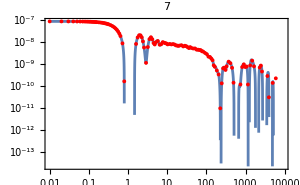
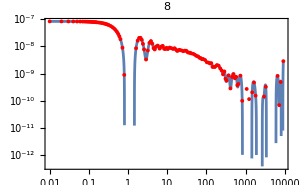

```mathematica
Table[Show[LogLogPlot[sacfInterpSAC3825[[id]][x],{x,0.01,Last[sac3825[[id,2]]]},ImageSize->300,PlotLabel->ToString[id]],ListLogLogPlot[Table[{sac3825[[id,2,i]],sac3825[[id,1,i]]},{i,Length[sac3825[[id,1]]]}],PlotStyle->Red]],{id,Length[sac3825]}]
```

```mathematica
sacCutoff3825={160,130,180,310,740,230,230,410,290,200};
```

```mathematica
viscosity3825=Table[NIntegrate[sacfInterpSAC3825[[i]][x],{x,0,sacCutoff3825[[i]]}],{i,10}]*4096/0.002
```

{1.4924,1.03521,1.29665,1.5482,2.02938,1.37765,1.39587,2.02706,1.88708,1.53534}

```mathematica
Mean[viscosity3825]
```

1.56249

```mathematica
StandardDeviation[viscosity3825]/Sqrt[10]
```

0.103046

### p_0=3.825 ,T=0.005

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00500000_waitingTime10000_idx13.nc"]
```

{/firstValue,/secondValue}

```mathematica
sac3825=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00500000_waitingTime10000_idx"<>ToString[i]<>".nc","Data"],{i,10,19}];
```

```mathematica
sacfInterpSAC3825=Table[Interpolation[Transpose[{Normal[sac3825[[i,2]]],Normal[sac3825[[i,1]]]}],Method->"Spline"],{i,10}];
```

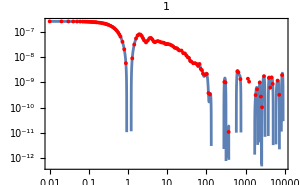
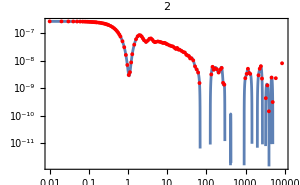
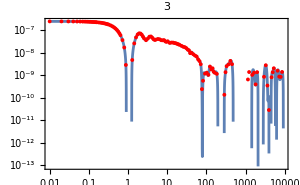
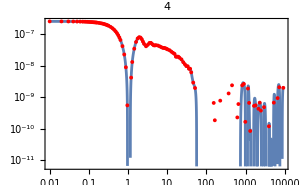
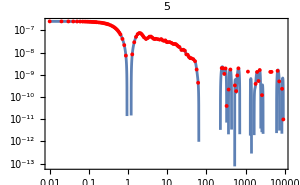
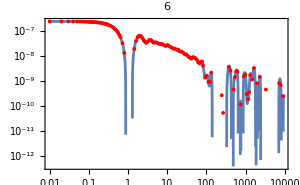
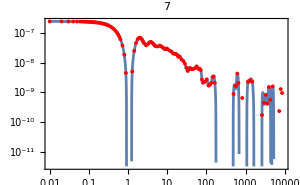
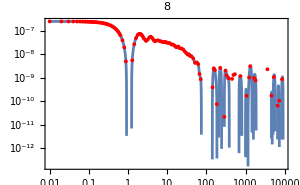

```mathematica
Table[Show[LogLogPlot[sacfInterpSAC3825[[id]][x],{x,0.01,Last[sac3825[[id,2]]]},ImageSize->300,PlotLabel->ToString[id]],ListLogLogPlot[Table[{sac3825[[id,2,i]],sac3825[[id,1,i]]},{i,Length[sac3825[[id,1]]]}],PlotStyle->Red]],{id,Length[sac3825]}]
```

```mathematica
sacCutoff3825={110,67,77,51,61,130,160,72,61,72};
```

```mathematica
viscosity3825=Table[NIntegrate[sacfInterpSAC3825[[i]][x],{x,0,sacCutoff3825[[i]]*1.5}],{i,10}]*4096/0.005
```

{1.0028,1.09162,1.10489,0.804322,0.784453,0.909894,0.983287,0.882681,0.710504,0.731885}

```mathematica
Mean[viscosity3825]
```

0.900633

```mathematica
StandardDeviation[viscosity3825]/Sqrt[10]
```

0.0451259

### p_0=3.75 ,T=0.02

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.750/SACtime_N4096_p3.7500_T0.02000000_waitingTime10000_idx12.nc"]
```

{/firstValue,/secondValue}

```mathematica
sac375=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.750/SACtime_N4096_p3.7500_T0.02000000_waitingTime10000_idx"<>ToString[i]<>".nc","Data"],{i,10,19}];
```

```mathematica
sacfInterpSAC375=Table[Interpolation[Transpose[{Normal[sac375[[i,2]]],Normal[sac375[[i,1]]]}],Method->"Spline"],{i,10}];
```

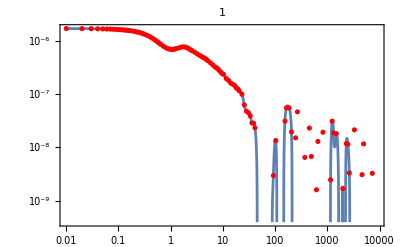
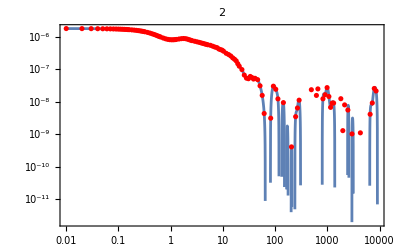
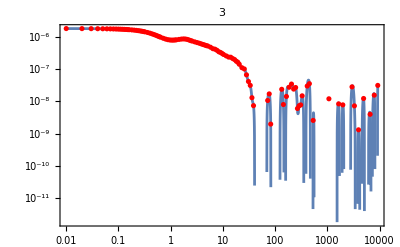
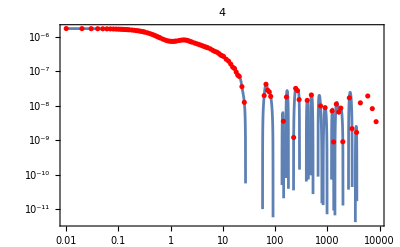
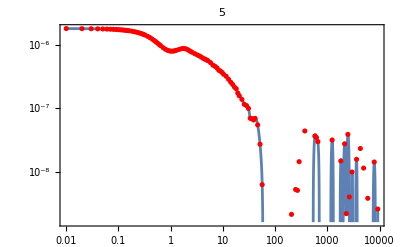
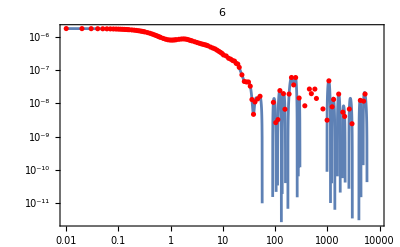
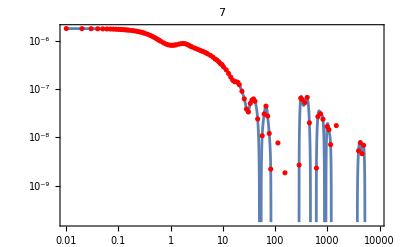
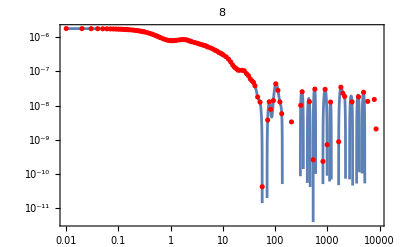

```mathematica
Table[Show[LogLogPlot[sacfInterpSAC375[[id]][x],{x,0.01,Last[sac375[[id,2]]]},ImageSize->400,PlotLabel->ToString[id]],ListLogLogPlot[Table[{sac375[[id,2,i]],sac375[[id,1,i]]},{i,Length[sac375[[id,1]]]}],PlotStyle->Red]],{id,Length[sac375]}]
```

```mathematica
sacCutoff375={41,28,36,26,56,46,28,56,24,36};
```

```mathematica
viscosity375=Table[NIntegrate[sacfInterpSAC375[[i]][x],{x,0,sacCutoff375[[i]]}],{i,10}]*4096/0.02
```

{1.59976,1.98601,1.87886,1.52091,2.36839,1.86661,1.78375,1.97165,1.61707,1.74344}

```mathematica
Mean[viscosity375]
```

1.83365

```mathematica
StandardDeviation[viscosity375]/Sqrt[10]
```

0.077559

## diffusion constant

### p_0=3.75 ,T=0.02

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityAutoCorrelation/velocityAutoCorrelationTime_N4096_p3.7500_T0.02000000_Cell_2_idx10.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

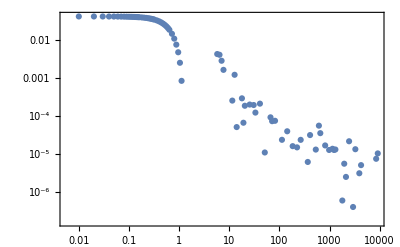

```mathematica
ListLogLogPlot[Table[{test[[2,i]],test[[1,i]]},{i,Length[test[[1]]]}]]
```

```mathematica
vac375=Table[Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityAutoCorrelation/velocityAutoCorrelationTime_N4096_p3.7500_T0.02000000_Cell_"<>ToString[i]<>"_idx"<>ToString[id+9]<>".nc","Data"],{i,0,4095}],{id,10}];
```

```mathematica
vac375[[1,1,2,1]]
```

0.

```mathematica
meanVac375=Table[Table[{vac375[[id,1,2,i]],Mean[Table[vac375[[id,cell,1,i]],{cell,Length[vac375[[id]]]}]]},{i,Length[vac375[[id,1,2]]]}],{id,10}];
```

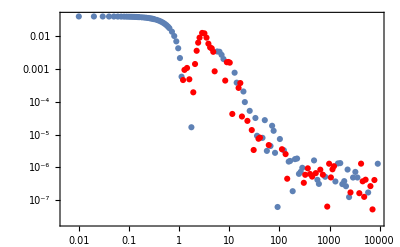
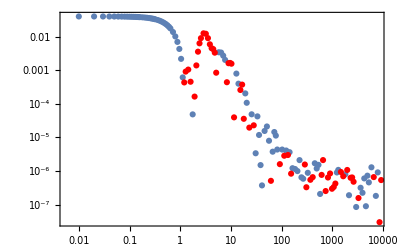
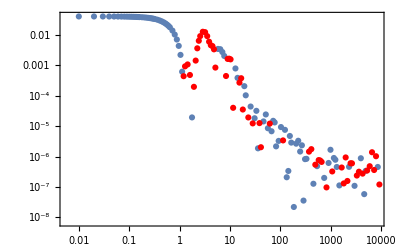
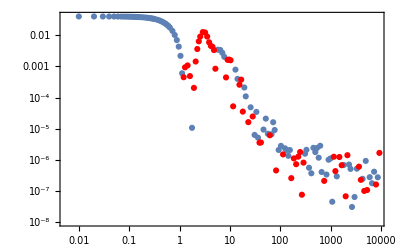
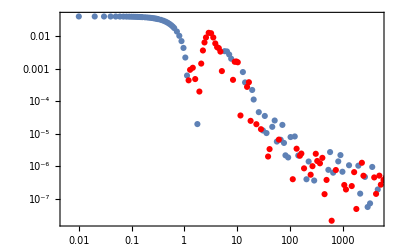
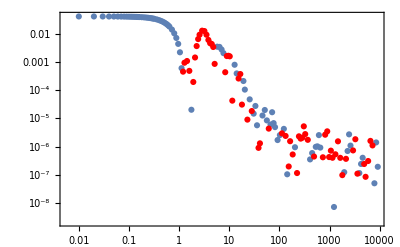
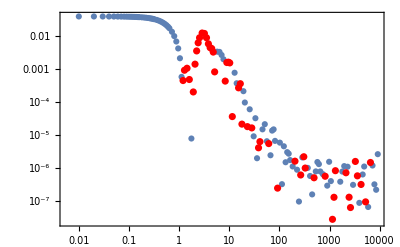
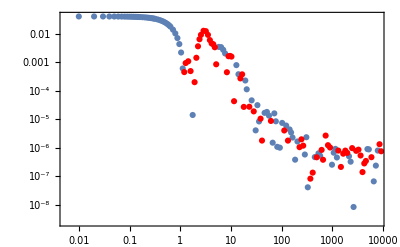

```mathematica
Table[Show[ListLogLogPlot[meanVac375[[id]],ImageSize->400],ListLogLogPlot[Table[{meanVac375[[id,t,1]],-meanVac375[[id,t,2]]},{t, Length[meanVac375[[id]]]}],PlotStyle->Red]],{id,10}]
```

```mathematica
cutoffs={310,150,300,150,180,110,300,180,200,270};
```

```mathematica
meanVacInterp375=Table[Interpolation[meanVac375[[id]],Method->"Spline"],{id,10}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

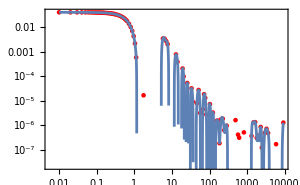
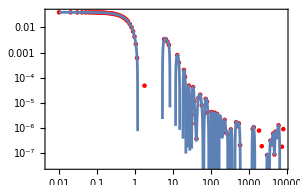
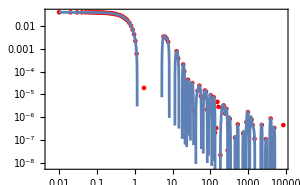
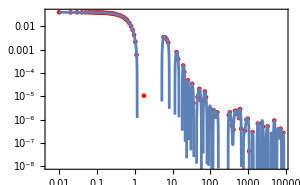
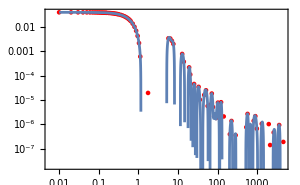
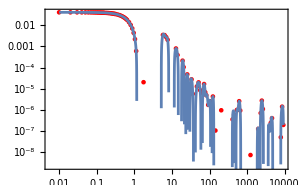
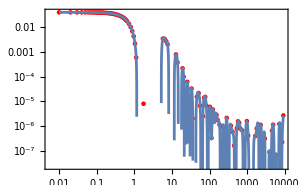
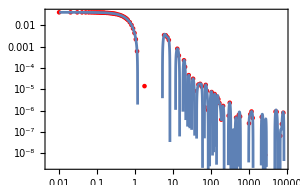

```mathematica
Table[Show[ListLogLogPlot[meanVac375[[id]],PlotStyle->Red,ImageSize->300],LogLogPlot[meanVacInterp375[[id]][x],{x,0.01,Last[meanVac375[[id]]][[1]]}]],{id,10}]
```

```mathematica
diffusionConstant375=Table[NIntegrate[meanVacInterp375[[id]][x],{x,0,cutoffs[[id]]}]/2,{id,10}]
```

{0.00387979,0.00394332,0.00407115,0.00383958,0.00391541,0.00389738,0.00397003,0.00390523,0.00395019,0.0040367}

```mathematica
Mean[diffusionConstant375]
```

0.00394088

```mathematica
StandardDeviation[diffusionConstant375]/Sqrt[10]
```

0.0000223355

### p_0=3.85 ,T=0.002

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityAutoCorrelation/velocityAutoCorrelationTime_N4096_p3.8500_T0.00200000_Cell_1404_idx13.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
ListLogLogPlot[Table[{test[[2,i]],test[[1,i]]},{i,Length[test[[1]]]}]]
```

-Graphics-

```mathematica
vac385=Table[Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityAutoCorrelation/velocityAutoCorrelationTime_N4096_p3.8500_T0.00200000_Cell_"<>ToString[i]<>"_idx"<>ToString[id+9]<>".nc","Data"],{i,0,4095}],{id,10}];
```

```mathematica
meanVac385=Table[Table[{vac385[[id,1,2,i]],Mean[Table[vac385[[id,cell,1,i]],{cell,Length[vac385[[id]]]}]]},{i,Length[vac385[[id,1,2]]]}],{id,10}];
```

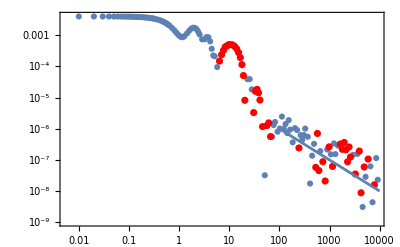
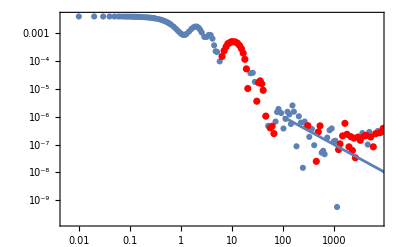
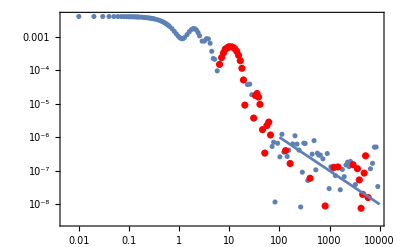
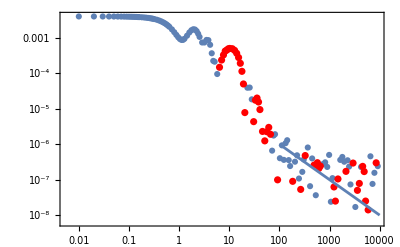
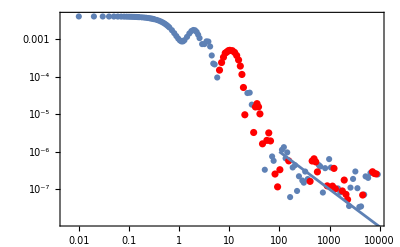
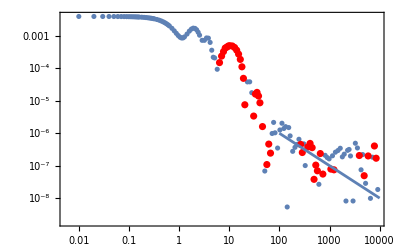
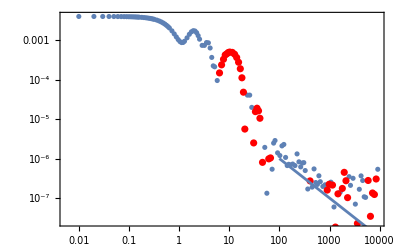
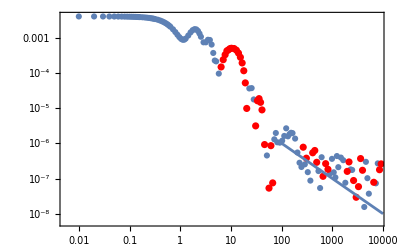

```mathematica
Table[Show[ListLogLogPlot[meanVac385[[id]],ImageSize->400],ListLogLogPlot[Table[{meanVac385[[id,t,1]],-meanVac385[[id,t,2]]},{t, Length[meanVac385[[id]]]}],PlotStyle->Red],LogLogPlot[0.0001x^(-1),{x,100,10000}]],{id,10}]
```

```mathematica
meanVacInterp385=Table[Interpolation[meanVac385[[id]],Method->"Spline"],{id,10}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

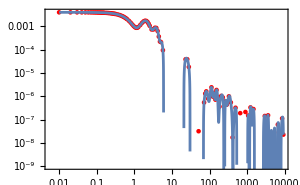
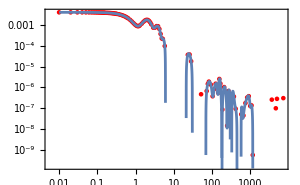
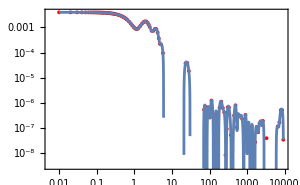
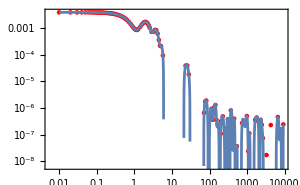
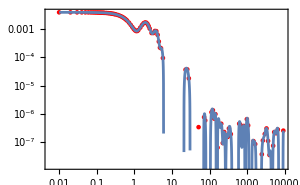
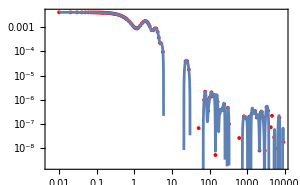
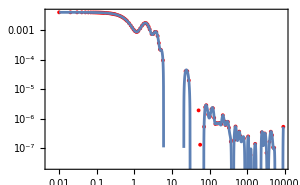
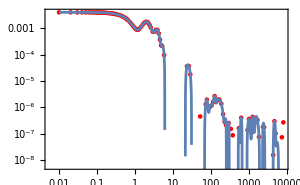

```mathematica
Table[Show[ListLogLogPlot[meanVac385[[id]],PlotStyle->Red,ImageSize->300],LogLogPlot[meanVacInterp385[[id]][x],{x,0.01,Last[meanVac385[[id]]][[1]]}]],{id,10}]
```

```mathematica
diffusionConstant385=Table[NIntegrate[meanVacInterp385[[id]][x],{x,0,150}]/2,{id,10}]
```

{0.00115367,0.00114571,0.00109234,0.00111243,0.00109467,0.00114905,0.00118704,0.00116642,0.00111476,0.00113999}

```mathematica
Mean[diffusionConstant385]
```

0.00113561

```mathematica
StandardDeviation[diffusionConstant385]/Sqrt[10]
```

5.28137×10^-6

### diffusion constant vs cutoff

```mathematica
dCDifferentCutoff=Table[Table[NIntegrate[meanVacInterp385[[id]][x],{x,0,cutoff}]/2,{id,10}],{cutoff,Table[10^(0.1*i-1),{i,0,50}]}];
```

```mathematica
meanDCDifferentCutoff=Table[Around[Mean[dCDifferentCutoff[[cutoff]]],StandardDeviation[dCDifferentCutoff[[cutoff]]]/Sqrt[10]],{cutoff,Length[dCDifferentCutoff]}]
```

{0.00019886310,0.00024955912,0.00031260216,0.00039043020,0.00048542927,0.000599304,0.000731905,0.000879497,0.0010325911,0.0011761916,0.0012978224,0.0014132433,0.00159754,0.00193214,0.00231885,0.00258536,0.00292697,0.00313718,0.00320059,0.002994311,0.002528513,0.001896315,0.001320914,0.001073313,0.001136620,0.001190226,0.001123127,0.001103330,0.0010965,0.0010995,0.0011087,0.0011259,0.0011400.000011,0.0011520.000012,0.0011660.000013,0.0011720.000014,0.0011810.000015,0.0011780.000016,0.0011760.000018,0.0011810.000019,0.0011930.000016,0.0012020.000017,0.0012160.000017,0.0012190.000023,0.0012160.000034,0.0012290.000033,0.001240.00004,0.001250.00004,0.001210.00005,0.001220.00006,0.001340.00021}

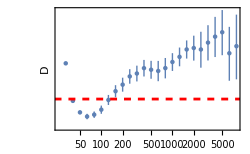

```mathematica
inset=Show[ListLogLogPlot[Table[{10^(0.1*i-1),meanDCDifferentCutoff[[i+1]]},{i,25,49}],ImageSize->250,FrameLabel->{"cutoff time", "D"}],LogLogPlot[0.001130.00014,{x,0.01,10000},PlotStyle->{Red,Dashed}]]
```

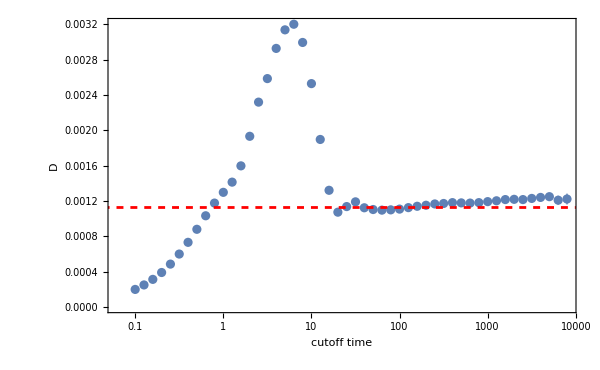

```mathematica
dvscutoffPlot=Show[ListLogLinearPlot[Table[{10^(0.1*i-1),meanDCDifferentCutoff[[i+1]]},{i,0,49}],ImageSize->600,FrameLabel->{"cutoff time", "D"}],LogLinearPlot[0.001130.00014,{x,0.01,10000},PlotStyle->{Red,Dashed}],Epilog->{Inset[inset,Scaled[{0.7,0.7}]]}]
```

```mathematica
Export["/home/chengling/Downloads/diffusionContantCutoff.jpeg",dvscutoffPlot,ImageResolution->200]
```

/home/chengling/Downloads/diffusionContantCutoff.jpeg